```mathematica
ClearAll["Global`*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Lynx paper notebook

## Script for analysis presented with respect to hoverfly flights

Karem Solanao Sanchez^1, Luis Robledo Ospina^(1,2) and Dinesh Rao^(1*)

1. Inbioteca, Universidad Veracruzana
2. School of Natural Sciences, Macquarie University
1*. vrao@uv.mx

# Trajectory analysis

## Preprocessing

### Load Trajectory3D package

Package available at Github, download and move to the Applications subdirectory of your user base directory.

```mathematica
$UserBaseDirectory
```

/Users/dinesh/Library/Wolfram

```mathematica
Get["/Users/dinesh/Library/Mobile Documents/com~apple~CloudDocs/mma packages/Trajectory/Trajectory3D.wl"]
Names["Trajectory3D`*"]
```

{AngleofFlight,CollettPlot3D,DistanceProfile3D,GetData3D,InputUserValues3D,OrthogonalComponentsVelocity3D,ProximityCut3D,SpeedCollettPlot3D,SpeedProfile3D,TwinCollettPlot3D}

### Import Data

project specific constants and other variables

```mathematica
fps = 1/500;(*frame rate*)
flyfolder = "/Users/dinesh/Dropbox/projects/lynx/lynx prey response/Data/processed data/flydata"; (*insert folder path to csv files *)

data=Import[#,"CSV"]&/@FileNames["*.csv",flyfolder];
```

#### Categorize data

```mathematica
flights=Range@Length@data
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27}

Assign flights to flower type

```mathematica
fyellows={2,3,16,17,18,19,20,21,22,23,24,25};
```

```mathematica
fwhites={1,4,5,6,7,8,9,10,11,12,13,14,15,26,27};
```

#### Segment trajectory to closest approach to flower (point chosen visually)

```mathematica
SpecialProximityCut3D[file_,n_]:=Module[{head,obj,cuts,cuttraj},
head=file[[All,{1,2,3}]];
obj=file[[All, {7,8,9}]];
cuts={75,282,119,90,58,285,328,242,471,311,117,85,404,257,75,497,65,328,245,250,118,53,54,182,258,10,19};
cuttraj=file[[;;cuts[[n]],All]];
cuttraj
]
```

```mathematica
mpc =SpecialProximityCut3D[data[[#]],#]&/@flights;
```

## Analyses

### Distance

Distance profile

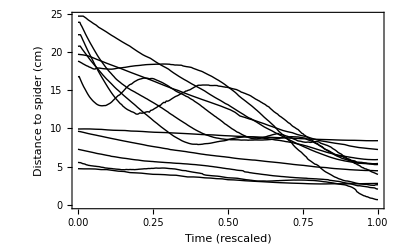

```mathematica
ListLinePlot[N@TimeSeriesRescale[DistanceProfile3D[mpc[[#]]], {0,1}]&/@fyellows, PlotStyle->Directive[{Black, Thin}], Frame->{{True,False},{True,False}},FrameLabel->{{HoldForm["Distance to spider (cm)"],None},{HoldForm["Time (rescaled)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

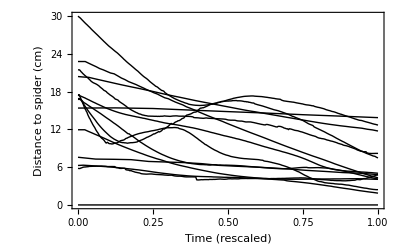

```mathematica
ListLinePlot[N@TimeSeriesRescale[DistanceProfile3D[mpc[[#]]], {0,1}]&/@fwhites[[2;;]], PlotStyle->Directive[{Black, Thin}], Frame->{{True,False},{True,False}},FrameLabel->{{HoldForm["Distance to spider (cm)"],None},{HoldForm["Time (rescaled)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotRange->All]
```

for fig

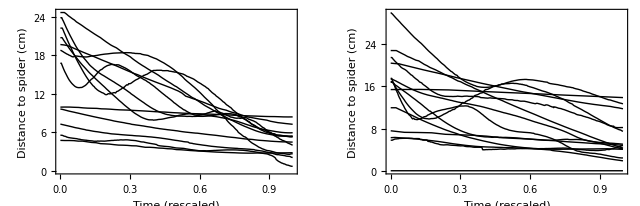

```mathematica
GraphicsRow[{,}]
```

minimum distance Yellows vs whites

```mathematica
minyellow= Min[DistanceProfile3D[mpc[[#]]]]&/@fyellows
```

{5.91197,4.46833,3.99423,7.24363,5.35963,2.55969,5.27143,5.38142,8.38861,2.74377,2.06915,0.689805}

```mathematica
minwhites= Min[DistanceProfile3D[mpc[[#]]]]&/@fwhites
```

{25.562,4.0714,11.7528,5.03334,3.83508,4.11694,2.42063,7.48262,1.87721,4.3131,8.17715,12.7003,3.71957×10^-12,13.8802,4.82305}

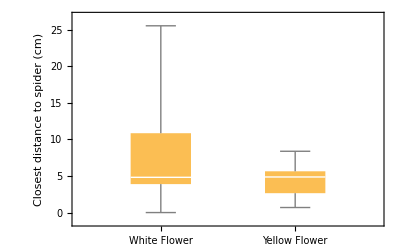

```mathematica
BoxWhiskerChart[{minwhites,minyellow},ChartLabels->{"White Flower","Yellow Flower"},FrameLabel->{{HoldForm["Closest distance to spider (cm)"],None},{None,None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Test whether the minimum distances are significantly different

```mathematica
Mean/@{minwhites,minyellow}
```

{7.33639,4.50681}

```mathematica
StandardDeviation/@{minwhites,minyellow}
```

{6.46878,2.2215}

```mathematica
MannWhitneyTest[{minwhites,minyellow},Automatic,"TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 76. | 0.48562

### Trajectory Plots

Plots of selected trajectories

Ball and pin plot of a typical trajectory

```mathematica
TwinCollettPlot3D[mpc[[4]]]
```

-Graphics3D-

```mathematica
Show[,ViewPoint->{1.3,-2.4,2.},Boxed->False]
```

-Graphics3D-

All trajectories (not run)

```mathematica
TwinCollettPlot3D[mpc[[#]]]&/@flights;
```

Colour coded to speed

```mathematica
SpeedCollettPlot3D[mpc[[4]]]
```

-Graphics3D-

### Distance vs Speed

```mathematica
yellowdistspeeds={DistanceProfile3D[mpc[[#]]],SpeedProfile3D[mpc[[#]]]}ᵀ&/@fyellows;
```

```mathematica
whitedistspeeds={DistanceProfile3D[mpc[[#]]],SpeedProfile3D[mpc[[#]]]}ᵀ&/@fwhites;
```

```mathematica
SmoothDensityHistogram[Flatten[yellowdistspeeds,1],PlotRange->{{0,30},{0,200}},FrameLabel->{{HoldForm["Speed (cm/s)"],None},{HoldForm["Distance from spider (cm)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
Export["/Users/dinesh/Desktop/yellowspeed.pdf",%106,"PDF"]
```

/Users/dinesh/Desktop/yellowspeed.pdf

Test for significance

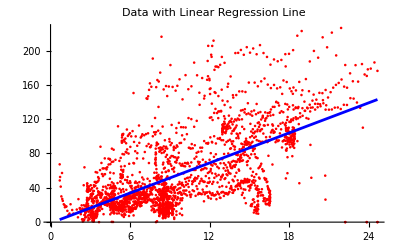

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.08304 | 1.60672 | -0.674068 | 0.500332
x | 5.83697 | 0.147782 | 39.497 | 3.80785×10^-264

```mathematica
(* Assuming yellowdistspeeds data is structured as {x, y} pairs *)
ydata=Flatten[yellowdistspeeds,1];

(* Fit a linear model *)
ymodel=LinearModelFit[ydata,x,x];

(* Show the plot with data and regression line *)
Show[
  ListPlot[ydata,PlotStyle->Red,PlotLabel->"Data with Linear Regression Line"],
  Plot[ymodel[x],{x,Min[ydata[[All,1]]],Max[ydata[[All,1]]]},PlotStyle->Blue]
]

(* Extract parameter significance *)
parameterTable=ymodel["ParameterTable"];
parameterTable
```

```mathematica
Grid[Transpose[{#,ymodel[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
```

AdjustedRSquared | 0.390045
AIC | 24475.6
BIC | 24493.
RSquared | 0.390295

```mathematica
SmoothDensityHistogram[Flatten[whitedistspeeds,1],PlotRange->{{0,30},{0,200}},FrameLabel->{{HoldForm["Speed (cm/s)"],None},{HoldForm["Distance from spider"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
Export["/Users/dinesh/Desktop/whitespeed.pdf",%107,"PDF"]
```

/Users/dinesh/Desktop/whitespeed.pdf

Test for significance

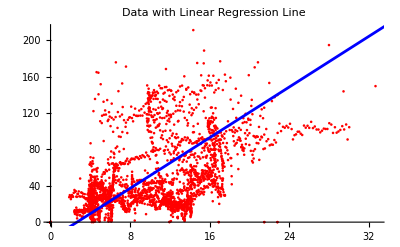

General::munfl: Exp[-1064.36] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -18.5431 | 1.59516 | -11.6246 | 1.52749×10^-30
x | 6.97139 | 0.123872 | 56.2792 | 0.

```mathematica
(* Assuming yellowdistspeeds data is structured as {x, y} pairs *)
wdata=Flatten[whitedistspeeds,1];

(* Fit a linear model *)
wmodel=LinearModelFit[wdata,x,x];

(* Show the plot with data and regression line *)
Show[
  ListPlot[wdata,PlotStyle->Red,PlotLabel->"Data with Linear Regression Line"],
  Plot[wmodel[x],{x,Min[wdata[[All,1]]],Max[wdata[[All,1]]]},PlotStyle->Blue]
]

(* Extract parameter significance *)
parameterTable=wmodel["ParameterTable"];
parameterTable
```

```mathematica
Grid[Transpose[{#,wmodel[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
```

AdjustedRSquared | 0.529725
AIC | 29525.2
BIC | 29543.
RSquared | 0.529892

For figure

```mathematica
GraphicsRow[{,}]
```

-Graphics-

```mathematica
Rasterize[%59,"Image"]
```

-Graphics-

```mathematica
Export["/Users/dinesh/Dropbox/projects/lynx/lynx prey response/Manuscript/Figures/distvsspeed_fly.pdf",%64,"PDF"]
```

/Users/dinesh/Dropbox/projects/lynx/lynx prey response/Manuscript/Figures/distvsspeed_fly.pdf

```mathematica
ListFitPlot[{ydata,wdata},PlotFit->"Linear", PlotRange->{{0,30},{0,300}}]
```

-Graphics-

controls ( data from control notebook)

```mathematica
ListFitPlot[{yc,wc},PlotFit->"Linear"]
```

-Graphics-

```mathematica
ListFitPlot[{yc,ydata, wc,wdata},PlotFit->"Linear", PlotRange->{{0,30},{0,300}}, PlotStyle->{StandardOrange,{Dashed,StandardOrange}, Blue, {Dashed,StandardBlue}},PlotFitElements->"None"]
```

-Graphics-

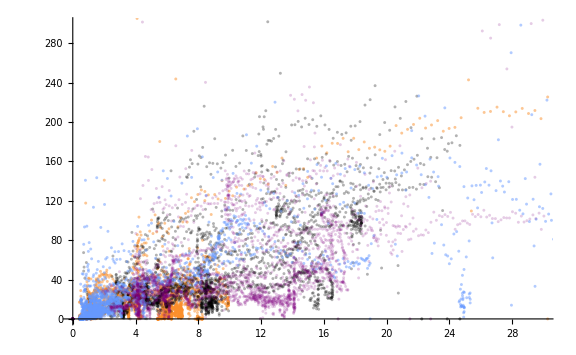

```mathematica
ListPlot[{yc,ydata,wc,wdata},
 PlotRange->{{0,30},{0,300}},
 PlotStyle->{Opacity[0.5,StandardOrange],Opacity[0.3,Black],Opacity[0.5,StandardBlue],Opacity[0.2,Purple]}]
```

```mathematica
Show[,,Frame->True,FrameLabel->{{"Speed (cm/s)",None},{"Distance to flower (cm)",None}},FrameTicks->{{All,None},{All,None}},FrameStyle->GrayLevel[0]]
```

-Graphics-

```mathematica
Export["/Users/dinesh/Desktop/Untitled.pdf",%395,"PDF"]
```

/Users/dinesh/Desktop/Untitled.pdf

```mathematica
SystemOpen["/Users/dinesh/Desktop/Untitled.pdf"]
```

```mathematica
SystemOpen["/Users/dinesh/Desktop/Untitled.tiff"]
```

### Persistence Velocity

#### Yellow flower flights

Extract persistent velocity values for yellow flower flights

```mathematica
PVyellows=OrthogonalComponentsVelocity3D[mpc[[#]]][[1]]&/@fyellows;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ypv = LowpassFilter[PVyellows[[#]],0.5]&/@ Range@Length@fyellows;
```

Distances for yellow flower flights

```mathematica
ydis=DistanceProfile3D[mpc[[#]]]&/@fyellows;
```

Join to a single dataset

```mathematica
yellowdistPV = {ydis[[#]][[2;;]],ypv[[#]]}ᵀ&/@{1,2,3,4,5,6,7,8,9,10,11,12};
```

Smooth density histogram with contours

```mathematica
SmoothDensityHistogram[Flatten[yellowdistPV,1],PlotRange->{{0,30},{-100,100}}, Mesh->30,FrameLabel->{{HoldForm[" Persistence Velocity (cm/s)"],None},{HoldForm["Distance from spider (cm)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

#### White flower flights

Extract persistent velocity values for white flower flights

```mathematica
PVwhites=OrthogonalComponentsVelocity3D[mpc[[#]]][[1]]&/@fwhites;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Subsample to remove trajectories where computation did not work; standardize (z-score normalisation) and then run a low pass filter

```mathematica
wpv = LowpassFilter[PVwhites[[#]],0.5]&/@ Range@Length@fwhites;
```

Distances for white flower flights

```mathematica
wdis=DistanceProfile3D[mpc[[#]]]&/@fwhites;
```

Join to a single dataset

```mathematica
whitedistPV = {wdis[[#]][[2;;]],wpv[[#]]}ᵀ&/@Range@Length@fwhites;
```

Smooth density histogram with contours

```mathematica
SmoothDensityHistogram[Flatten[whitedistPV,1],PlotRange->{{0,30},{-100,100}}, Mesh->20,FrameLabel->{{HoldForm["Persistence Velocity (cm/s)"],None},{HoldForm["Distance to spider (cm)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

For figure

```mathematica
GraphicsRow[{,}]
```

-Graphics-

### Angle of flight

# Visual Modelling

## Import data

```mathematica
hv=Import["/Users/dinesh/Dropbox/projects/lynx/lynx prey response/QCPA/hoverflytop.csv"]
```

{{Flower,Distance,LuminanceCon,ChromaticityCon,KurtosisChrom,KurtosisLum},{White,10,7.576,2.661,34.917,16.305},{White,5,7.742,2.65,51.761,24.335},{White,2,7.895,2.753,89.358,51.819},{White,10,8.01,2.954,23.991,10.158},{White,5,8.137,2.831,31.719,13.814},{White,2,8.169,2.946,39.722,17.332},{White,10,6.401,2.759,32.139,17.149},{White,5,6.516,2.644,54.63,24.948},{White,2,6.588,2.649,85.735,40.725},{White,10,7.351,2.62,25.928,11.356},{White,5,7.138,2.476,32.192,15.854},{White,2,6.881,2.48,41.644,20.785},{White,10,6.793,2.887,29.344,15.215},{White,5,6.849,2.87,39.597,19.133},{White,2,6.789,2.822,51.651,24.941},{Yellow,10,3.412,4.984,14.764,19.422},{Yellow,5,3.552,5.151,19.63,30.445},{Yellow,2,3.716,5.957,35.849,57.239},{Yellow,10,4.917,6.809,8.342,9.209},{Yellow,5,4.952,6.935,12.377,15.37},{Yellow,2,5.181,7.162,15.446,25.958},{Yellow,10,3.988,5.382,10.196,10.348},{Yellow,5,4.172,5.769,15.306,18.832},{Yellow,2,4.213,5.743,20.004,33.12},{Yellow,10,4.721,6.269,5.087,8.099},{Yellow,5,4.85,6.409,7.396,12.206},{Yellow,2,5.076,6.445,9.194,19.197},{Yellow,10,4.481,6.692,5.455,9.758},{Yellow,5,4.677,6.979,7.969,15.993},{Yellow,2,4.858,7.013,10.297,24.215}}

```mathematica
hvdata = hv[[2;;]];
```

### Luminance Contrast

```mathematica
lumcon=GroupBy[hvdata,{#[[2]]&,First},#[[3]]&/@#&];
```

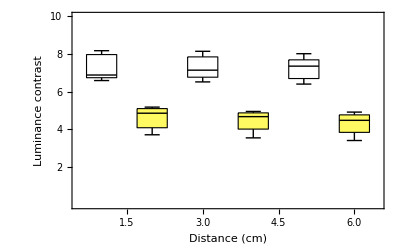

```mathematica
boxplotData=Flatten[Table[{lumcon[num,"White"],lumcon[num,"Yellow"]},{num,{2,5,10}}],1];

BoxWhiskerChart[boxplotData,{{"Whiskers",Black},{"Fences",Thin},{"MedianMarker",Black}},ChartStyle->{White, RGBColor[1., 0.98, 0.38]},Frame->True,PlotRange->{Automatic,{0,10}},FrameLabel->{{"Luminance contrast",None},{"Distance (cm)",None}},FrameTicks->{{{2,4,6,8,10},None},{Automatic,None}}, FrameStyle->Black,ChartBaseStyle->EdgeForm[Black],Ticks->None,LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]}]
```

### Chromatic Contrast

```mathematica
chromcon=GroupBy[hvdata,{#[[2]]&,First},#[[4]]&/@#&];
```

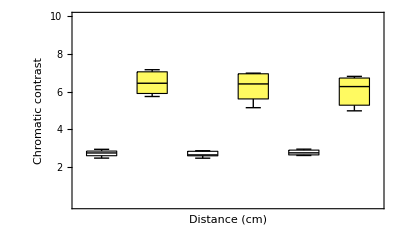

```mathematica
boxplotDatac=Flatten[Table[{chromcon[num,"White"],chromcon[num,"Yellow"]},{num,{2,5,10}}],1];

BoxWhiskerChart[boxplotDatac,{{"Whiskers",Black},{"Fences",Thin},{"MedianMarker",Black}},ChartStyle->{White, RGBColor[1., 0.98, 0.38]},Frame->True,PlotRange->{Automatic,{0,10}},ChartBaseStyle->EdgeForm[Black], FrameStyle->Black,FrameLabel->{{"Chromatic contrast",None},{"Distance (cm)",None}},FrameTicks->{{{2,4,6,8,10},None},{Automatic,None}},LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]}]
```

### Chromatic Kurtosis

```mathematica
ChrKurt=GroupBy[hvdata,{#[[2]]&,First},#[[5]]&/@#&];
```

```mathematica
boxplotDatack=Flatten[Table[{ChrKurt[num,"White"],ChrKurt[num,"Yellow"]},{num,{2,5,10}}],1];
```

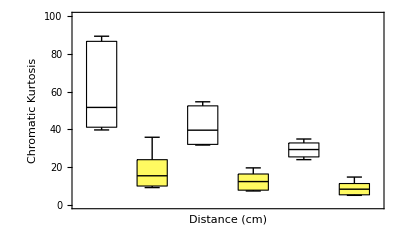

```mathematica
BoxWhiskerChart[boxplotDatack,{{"Whiskers",Black},{"Fences",Thin},{"MedianMarker",Black}},ChartStyle->{White, RGBColor[1., 0.98, 0.38]},Frame->True,PlotRange->{Automatic,{0,100}},ChartBaseStyle->EdgeForm[Black], FrameStyle->Black,FrameLabel->{{"Chromatic Kurtosis",None},{"Distance (cm)",None}},FrameTicks->{{{0,20,40,60,80,100},None},{Automatic,None}},LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]}]
```

### Luminance Kurtosis

```mathematica
LumKurt=GroupBy[hvdata,{#[[2]]&,First},#[[6]]&/@#&];
```

```mathematica
boxplotDatalk=Flatten[Table[{LumKurt[num,"White"],LumKurt[num,"Yellow"]},{num,{2,5,10}}],1];
```

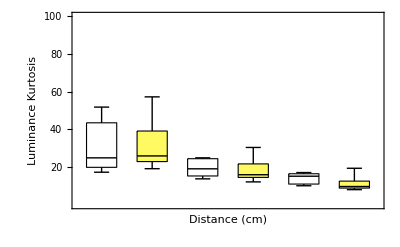

```mathematica
BoxWhiskerChart[boxplotDatalk,{{"Whiskers",Black},{"Fences",Thin},{"MedianMarker",Black}},ChartStyle->{White, RGBColor[1., 0.98, 0.38]},Frame->True,PlotRange->{Automatic,{0,100}},ChartBaseStyle->EdgeForm[Black], FrameStyle->Black,FrameLabel->{{"Luminance Kurtosis",None},{"Distance (cm)",None}},FrameTicks->{{{20,40,60,80,100},None},{Automatic,None}},LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]}]
```

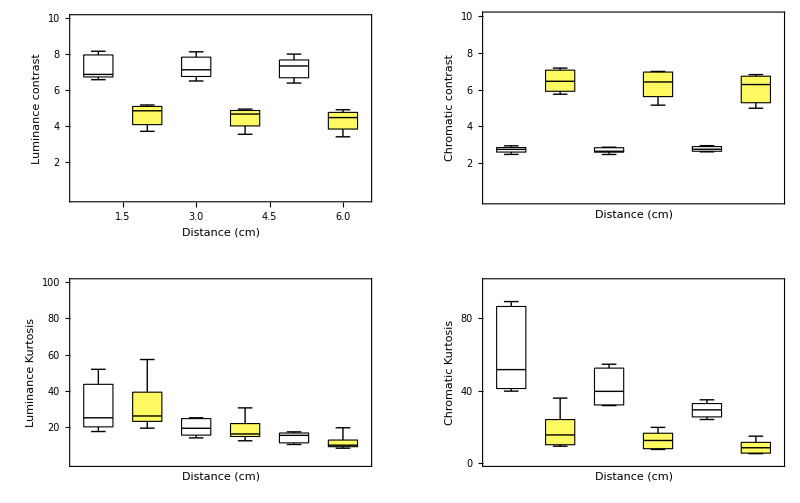

```mathematica
GraphicsGrid[{{,},{,}}]
```